# Wind Turbine Designer Tool

## Math Model

### Constants

#### Air Density (δa)

```mathematica
δa=1.225;
```

```mathematica
CPmax = 0.5925925925925926;
```

### Equations

#### Wind Power

```mathematica
Pw[Vw_, R_, CP_]:= 1/2 CP δa Vw^3 R^2 π;
```

#### Rotor radius

```mathematica
RotorRadius[Po_,  Vw_, Cp_]:=√((2*Po)/(δa * Vw^3*Cp * π));
```

#### Tip Speed Ratio (λ)

```mathematica
TSR[Vw_, rpm_, R_]:= R*rpm*π / (Vw * 30);
```

#### Revolutions Per Minutes

```mathematica
RPM[Vw_, λ_,  R_]:= (λ * 30 * Vw)/(R*π);
```

```mathematica
RPM2[Vw_, rpmmax_,λ_,R_]:= Piecewise[{{RPM[Vw,λ, R], RPM[Vw,λ, R] ≤rpmmax  }, {rpmmax,  RPM[Vw,λ, R]>rpmmax}}]
```

#### Average Chord Length

```mathematica
AverageChordLength[R_,Sp_,Cl_,Z_]:=(R * Sp)/(Cl * Z);
```

#### Chord Length List

```mathematica
ChordLength[R_, Vw_, Z_, Cl_, λ_, Vr_]:=(2 π R 8 Vw)/(Z 9 Cl λ Vr);
```

#### Solidity

```mathematica
Solidity[R_,l_,Z_]:=(Z*l)/(π*R);
```

#### Blade Velocity

```mathematica
Vu[ R_, rpm_]:=R*rpm*π/30;
```

#### Relative Wind Velocity

```mathematica
Vr[Vw_, Vu_]:=√((2/3 Vw)^2+ Vu^2);
```

#### Wind Angle (θ)

```mathematica
theta[λr_]:=ArcTan[2/(3 λr)]/ Degree;
```

#### Forces on the Blade

```mathematica
Fblade[CFT_, Vr_, L_, dr_]:=1/2 CFT δa Vr^2 L dr;
```

## Airfoil Data

### Airfoil Specifications: A18

#### Aerodynamic Data

```mathematica
A18AlphaData=List[-9.5,-9.25,-9.0,-8.75,-8.5,-8.25,-8.0,-7.75,-7.5,-7.25,-7.0,-6.75,-6.5,-6.25,-6.0,-5.75,-5.5,-5.25,-5.0,-4.75,-4.5,-4.25,-4.0,-3.75,-3.5,-3.25,-3.0,-2.75,-2.5,-2.25,-2.0,-1.75,-1.5,-1.25,-1.0,-0.75,-0.5,-0.25,0.0,0.25,0.5,0.75,1.0,1.25,1.5,1.75,2.0,2.25,2.5,2.75,3.0,3.25,3.5,3.75,4.0,4.25,4.5,4.75,5.0,5.25,5.5,5.75,6.0,6.25,6.5,6.75,7.0,7.25,7.5,7.75,8.0,8.25,8.5,8.75,9.0,9.25,9.5,9.75,10.0,10.25,10.5,10.75,11.0,11.25,11.5,11.75,12.0,12.25,12.5];
A18CLData=List[-0.4443,-0.4551,-0.4655,-0.4733,-0.4792,-0.4593,-0.431,-0.4061,-0.3775,-0.3422,-0.307,-0.2723,-0.2369,-0.2006,-0.1662,-0.1313,-0.0951,-0.0624,-0.0272,0.0096,0.0415,0.0754,0.1105,0.1409,0.1742,0.2073,0.2383,0.2721,0.3022,0.334,0.365,0.395,0.4255,0.4552,0.4838,0.5113,0.5352,0.5594,0.5876,0.615,0.6424,0.6695,0.6965,0.7235,0.7503,0.7769,0.8032,0.8295,0.8553,0.881,0.9061,0.9306,0.9524,0.9755,0.9928,1.0127,1.0353,1.0573,1.0767,1.0964,1.1174,1.1387,1.1585,1.1746,1.1923,1.2095,1.2269,1.2443,1.2608,1.2761,1.2905,1.3036,1.3151,1.3252,1.3333,1.3375,1.3364,1.3326,1.3263,1.3179,1.3064,1.2937,1.2783,1.2608,1.2421,1.2217,1.2003,1.1776,1.154];
A18CDData=List[0.086,0.08249,0.07857,0.07371,0.06745,0.02683,0.02267,0.02145,0.02003,0.01853,0.01806,0.01798,0.01752,0.01752,0.01749,0.01659,0.01593,0.01542,0.01483,0.01429,0.01368,0.01323,0.01285,0.01257,0.01222,0.01194,0.01166,0.01138,0.01115,0.01091,0.01074,0.01055,0.01032,0.01014,0.00984,0.00951,0.00905,0.00868,0.00876,0.00887,0.009,0.00914,0.00931,0.00949,0.00967,0.00988,0.0101,0.01034,0.01062,0.01092,0.01127,0.01165,0.01225,0.01282,0.01405,0.01509,0.01578,0.01652,0.01761,0.01869,0.0196,0.02042,0.02142,0.02285,0.02402,0.02525,0.02649,0.02768,0.02898,0.03054,0.03232,0.03452,0.03746,0.04029,0.04266,0.04499,0.04725,0.04975,0.05252,0.05553,0.0591,0.06296,0.06751,0.07275,0.07869,0.08555,0.09339,0.10243,0.11286];
```

#### Lift Coefficient (CL) in function of attact angle (α)

```mathematica
A18FCL = Interpolation[Thread[{A18AlphaData, A18CLData}]];
```

#### Drag Coefficient (CD) in function of attact angle (α)

```mathematica
A18FCD= Interpolation[Thread[{A18AlphaData, A18CDData}]];
```

#### Plotting Functions

```mathematica
Show[ Plot[{Labeled[A18FCL[α],"CL"], Labeled[A18FCD[α],"CD"]},{α, -9.5, 12.5}, AxesLabel->{"Angel α","Coefficient"}]]
```

-Graphics-

#### Airfoil Geometry

```mathematica
A18Geometry = List[{1.00000000,0.00614000},{0.94999999,0.01817000},{0.89999998,0.02858000},{0.80000001,0.04624000},{0.69999999,0.06056000},{0.60000002,0.07197000},{0.55000001,0.07612000},{0.50000000,0.07975000},{0.44999999,0.08293000},{0.40000001,0.08376000},{0.34999999,0.08466000},{0.30000001,0.08383000},{0.25000000,0.08065000},{0.20000000,0.07601000},{0.15000001,0.07026000},{0.10000000,0.06234000},{0.07500000,0.05660000},{0.05000000,0.04923000},{0.02500000,0.03947000},{0.01250000,0.03239000},{0.00000000,0.01865000},{0.01250000,0.00781000},{0.02500000,0.00357000},{0.05000000,0.00075000},{0.07500000,0.00000000},{0.10000000,0.00006000},{0.15000001,0.00200000},{0.20000000,0.00475000},{0.25000000,0.00806000},{0.30000001,0.01038000},{0.34999999,0.01353000},{0.40000001,0.01657000},{0.44999999,0.01780000},{0.50000000,0.01884000},{0.55000001,0.01980000},{0.60000002,0.01998000},{0.69999999,0.01924000},{0.80000001,0.01452000},{0.89999998,0.00813000},{0.94999999,0.00434000},{1.00000000,0.00000000}];
```

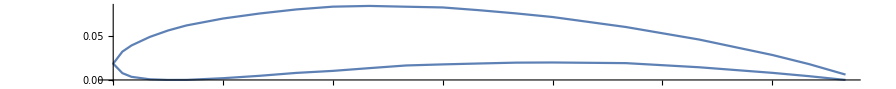

```mathematica
ListLinePlot[A18Geometry, AspectRatio->.1]
```

## Designer

### Design Parameters

#### Air Velocity

```mathematica
Vw = 15;
```

#### Proposed RPM

```mathematica
rpm1 =750;
```

#### Number of Blades

```mathematica
Z1 = 3;
```

#### Number of Ribs (Blade Sections)

```mathematica
Nr = 20;
```

#### Design Power

```mathematica
Pd = 5000;
```

### Common Calculations

#### Calculate the rotor radius

```mathematica
R1 = Round[RotorRadius[Pd, Vw , .45], .01]
```

1.31

#### Calculate the “Tip Speed Ratio” (λ)

```mathematica
λd = TSR[Vw, rpm1, R1]
```

6.85914

```mathematica
TSRD[V_]:= Piecewise[{{λd,RPM[V,λd, R1] ≤ rpm1},{ TSR[V, rpm1, R1],RPM[V,λd, R1] > rpm1}}];
```

#### Differential of the radius (Δr)

```mathematica
Δr =(R1 - 0.10*R1) / (Nr -1)
```

0.0620526

#### Vector of ribs radius

```mathematica
Rb = Table[x,{x,R1 - Δr*(Nr-1),  R1,Δr  }]
```

{0.131,0.193053,0.255105,0.317158,0.379211,0.441263,0.503316,0.565368,0.627421,0.689474,0.751526,0.813579,0.875632,0.937684,0.999737,1.06179,1.12384,1.18589,1.24795,1.31}

#### Calculating the blade velocity list

```mathematica
Vus1 =Vu[Rb, rpm1]
```

{10.2887,15.1623,20.0359,24.9095,29.7831,34.6567,39.5303,44.4039,49.2775,54.1511,59.0247,63.8983,68.7719,73.6455,78.5191,83.3928,88.2664,93.14,98.0136,102.887}

#### Calculating the relative wind velocity list

```mathematica
Vrs1 = Vr[Vw ,Vus1]
```

{14.3477,18.163,22.3928,26.8418,31.4171,36.0706,40.7756,45.516,50.282,55.0667,59.8658,64.6761,69.4952,74.3214,79.1534,83.9902,88.831,93.6752,98.5224,103.372}

#### Calculating the speed ratio list

```mathematica
λr1  = λd *Rb /R1
```

{0.685914,1.01082,1.33573,1.66063,1.98554,2.31045,2.63536,2.96026,3.28517,3.61008,3.93498,4.25989,4.5848,4.9097,5.23461,5.55952,5.88442,6.20933,6.53424,6.85914}

#### Calculating the relative air angle

```mathematica
θs1 = theta[λr1]
```

{44.1847,33.406,26.5239,21.8731,18.56,16.0952,14.1963,12.6916,11.4714,10.4628,9.61577,8.89456,8.27329,7.73265,7.25797,6.83794,6.46368,6.1281,5.82554,5.55136}

#### Common Parameters

```mathematica
getMaxValue1[function_]:=FindMaximum[{function, α ≥ αlim2 && α ≤ αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[1]];
```

```mathematica
getMaxValue2[function_]:=α/. FindMaximum[{function, α ≥ αlim2 && α ≤ αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[2]];
```

### Airfoil A18

#### “Tangential Force Coefficient” (CFT) and “Normal Force Coefficient “(CFN) in function of attack angle “α” and the speed ratio “λ”

```mathematica
A18CFT[α_, λ_]:= A18FCL[α]* Sin[theta[λ] Degree] - A18FCD[α]* Cos[theta[λ] Degree]
A18CFN[α_, λ_]:=  A18FCL[α]* Cos[theta[λ] Degree] + A18FCD[α]* Sin[theta[λ] Degree]
```

```mathematica
Plot3D[{A18CFT[α,λ], A18CFN[α,λ]},{α,-9,12},{λ,0,λd}]
```

-Graphics3D-

#### Max attact angle

```mathematica
αlim1 = 18;
αlim2 = -8;
```

```mathematica
A18MaxAngle=α/. FindMaximum[{A18FCL[α], α ≥αlim2 && α ≤αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[2]]
```

InterpolatingFunction::dmval: Input value {17.9649} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {17.9647} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {17.965} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

18.

#### Calculating the chord length

```mathematica
A18Length= AverageChordLength[R1, .3,A18FCL[A18MaxAngle], Z1]
```

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.107668

#### Calculating the solidity

```mathematica
A18Solidity = Solidity[R1,A18Length,Z1]
```

0.0784852

#### Calculating the maximum CL for speed ratio

```mathematica
A18MaxCFT = Map[getMaxValue1,A18CFT[α,λr1]]
```

InterpolatingFunction::dmval: Input value {14.6595} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.899963,0.698987,0.557399,0.457148,0.38395,0.328736,0.286308,0.252729,0.225428,0.202812,0.183811,0.167638,0.153717,0.141617,0.131012,0.121643,0.113313,0.105872,0.0991843,0.0931377}

#### Calculating the angle for the maximum CL for speed ratio

```mathematica
A18MaxAlpha = Map[getMaxValue2,A18CFT[α,λr1]]
```

InterpolatingFunction::dmval: Input value {14.6595} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{9.2217,9.16413,9.1017,9.03325,8.97776,8.87811,8.35179,8.26178,8.24754,8.19045,8.13546,8.08159,8.0278,7.9652,7.90875,7.85061,7.78906,7.68284,7.62361,7.57078}

#### Calculating the pitch angle

```mathematica
A18Beta =(θs1 -A18MaxAlpha)
```

{34.963,24.2419,17.4222,12.8399,9.58226,7.21708,5.84452,4.4298,3.22384,2.2724,1.48031,0.812971,0.245492,-0.232558,-0.650779,-1.01267,-1.32539,-1.55474,-1.79807,-2.01942}

#### Calculating the chords

```mathematica
A18lengthList = ChordLength[Rb,Vw, Z1, A18FCL[A18MaxAngle], λr1, Vrs1]
```

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.305514,0.241339,0.195752,0.163306,0.139524,0.121524,0.107502,0.0963054,0.0871772,0.0796023,0.0732211,0.0677753,0.0630755,0.0589796,0.0553791,0.0521899,0.0493458,0.046794,0.0444918,0.0424045}

#### Showing the results in table form

```mathematica
Thread[{Rb,A18lengthList,A18Beta }] //TableForm
```

0.131 | 0.305514 | 34.963
0.193053 | 0.241339 | 24.2419
0.255105 | 0.195752 | 17.4222
0.317158 | 0.163306 | 12.8399
0.379211 | 0.139524 | 9.58226
0.441263 | 0.121524 | 7.21708
0.503316 | 0.107502 | 5.84452
0.565368 | 0.0963054 | 4.4298
0.627421 | 0.0871772 | 3.22384
0.689474 | 0.0796023 | 2.2724
0.751526 | 0.0732211 | 1.48031
0.813579 | 0.0677753 | 0.812971
0.875632 | 0.0630755 | 0.245492
0.937684 | 0.0589796 | -0.232558
0.999737 | 0.0553791 | -0.650779
1.06179 | 0.0521899 | -1.01267
1.12384 | 0.0493458 | -1.32539
1.18589 | 0.046794 | -1.55474
1.24795 | 0.0444918 | -1.79807
1.31 | 0.0424045 | -2.01942

#### Plotting the twist

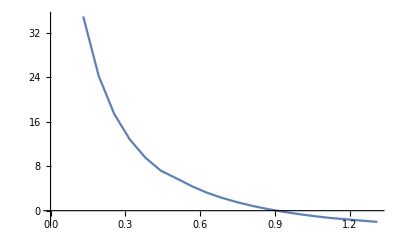

```mathematica
ListLinePlot[Thread[{Rb,A18Beta}]]
```

#### Plotting the chord length

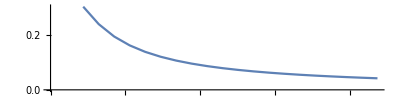

```mathematica
ListLinePlot[Thread[{Rb,A18lengthList}], AspectRatio->.25]
```

## Power Generation

### Common Calculations

#### Averaged Sections

```mathematica
For[i = 1; Rb2 = {}, i < Length[Rb], i++, AppendTo[Rb2, (Rb[[i]] + Rb[[i + 1]]) /2]]
Rb2
```

{0.162026,0.224079,0.286132,0.348184,0.410237,0.472289,0.534342,0.596395,0.658447,0.7205,0.782553,0.844605,0.906658,0.968711,1.03076,1.09282,1.15487,1.21692,1.27897}

#### Speed Ratio for Averaged Sections

```mathematica
λr2 =λd Rb2 / R1
```

{0.848368,1.17327,1.49818,1.82309,2.148,2.4729,2.79781,3.12272,3.44762,3.77253,4.09744,4.42234,4.74725,5.07216,5.39706,5.72197,6.04688,6.37178,6.69669}

### Airfoil A18

#### Average Length Sections

```mathematica
For[i = 1; A18lengthList2 = {}, i < Length[A18lengthList], i++, AppendTo[A18lengthList2, (A18lengthList[[i]] + A18lengthList[[i + 1]]) /2]]
A18lengthList2
```

{0.273427,0.218545,0.179529,0.151415,0.130524,0.114513,0.101904,0.0917413,0.0833898,0.0764117,0.0704982,0.0654254,0.0610275,0.0571793,0.0537845,0.0507679,0.0480699,0.0456429,0.0434482}

#### Average Pitch Angles

```mathematica
For[i = 1; A18Beta2  = {}, i < Length[A18Beta], i++, AppendTo[A18Beta2 , (A18Beta[[i]] + A18Beta[[i + 1]]) /2]]
A18Beta2
```

{29.6025,20.8321,15.1311,11.2111,8.39967,6.5308,5.13716,3.82682,2.74812,1.87636,1.14664,0.529232,0.00646681,-0.441669,-0.831725,-1.16903,-1.44006,-1.6764,-1.90874}

#### Forces along the blade

```mathematica
A18TFList = Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr];
```

```mathematica
A18NFList = Fblade[A18CFN[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr];
```

```mathematica
A18TF[V_]:=Piecewise[{
{ Total[Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[V, V λr2], A18lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[A18CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-A18Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], A18lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
A18NF[V_]:=Piecewise[{
{ Total[Fblade[A18CFN[theta[λr2]-A18Beta2, λr2], Vr[V, V λr2], A18lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[A18CFN[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-A18Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], A18lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
A18CT[V_]:= (2 A18TF[V])/(δa π V^2 R1^2)
```

#### Out Power

```mathematica
A18Po[V_]:=Piecewise[{
{ (Z1 π)/30 RPM[V, λd, R1] Total[Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[V, V λr2], A18lengthList2, Δr] Rb2],  RPM[V,λd, R1] ≤ rpm1 },

{ (Z1 π)/30 rpm1 Total[Fblade[A18CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-A18Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], A18lengthList2, Δr] Rb2],  RPM[V,λd, R1] > rpm1 }
}]
```

```mathematica
A18Po[Vw]
```

5761.5

```mathematica
Pw[Vw, R1, 1]
```

11144.8

```mathematica
A18Po[Vw]/Pw[Vw, R1, 1]
```

0.516967

```mathematica
A18Po[15]/Pw[15, R1, 1]
```

0.516967

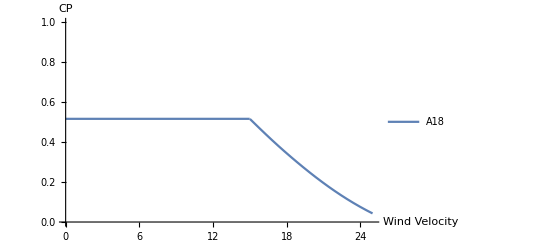

```mathematica
Plot[{A18Po[v]/Pw[v, R1, 1]} ,{v,0,Vw +10}, PlotRange->{0,1},AxesLabel->{"Wind Velocity", "CP"} ,PlotLegends->{"A18"}]
```

### Chart

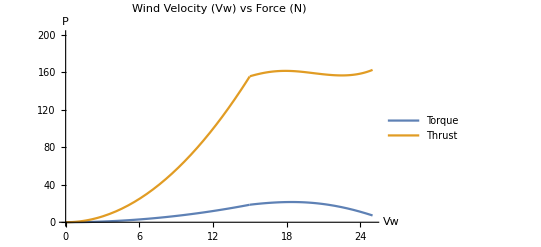

```mathematica
Plot[{A18TF[v], A18NF[v]} ,{v,0,Vw +10}, PlotRange->{0,200},PlotLabel->Style["Wind Velocity (Vw) vs Force (N)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["Vw", Black,20,FontFamily->"Times New Roman"], Style["P", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"Torque","Thrust"}]
```

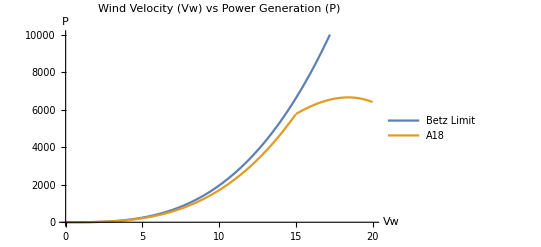

```mathematica
Plot[{Pw[v, R1, CPmax], A18Po[v]} ,{v,0,Vw +5}, PlotRange->{0,10000},PlotLabel->Style["Wind Velocity (Vw) vs Power Generation (P)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["Vw", Black,20,FontFamily->"Times New Roman"], Style["P", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"Betz Limit","A18"}]
```

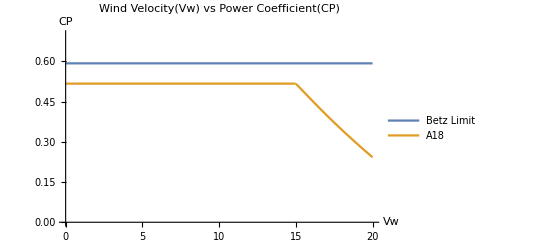

```mathematica
Plot[{Pw[v, R1, CPmax]/Pw[v, R1, 1],A18Po[v]/Pw[v, R1, 1]} ,{v,0,Vw +5}, PlotRange->{0,.7},PlotLabel->Style["Wind Velocity(Vw) vs Power Coefficient(CP)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["Vw", Black,20,FontFamily->"Times New Roman"], Style["CP", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"Betz Limit","A18"}]
```

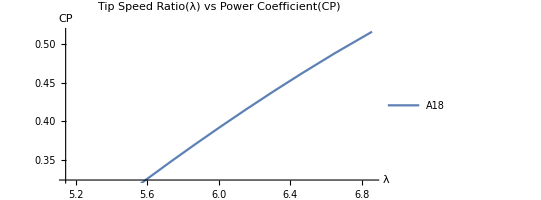

```mathematica
ParametricPlot[{TSRD[v],A18Po[v]/Pw[v, R1, 1]} ,{v,0,Vw +5},PlotLabel->Style["Tip Speed Ratio(λ) vs Power Coefficient(CP)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["λ", Black,20,FontFamily->"Times New Roman"], Style["CP", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"A18"}, AspectRatio->1/2]
```

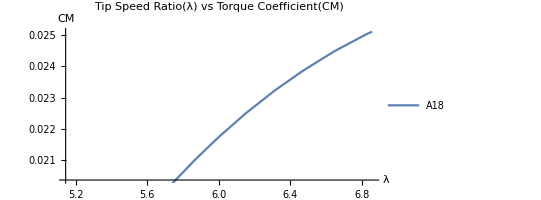

```mathematica
ParametricPlot[{TSRD[v],A18CT[v]} ,{v,0,Vw +5},PlotLabel->Style["Tip Speed Ratio(λ) vs Torque Coefficient(CM)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["λ", Black,20,FontFamily->"Times New Roman"], Style["CM", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"A18"}, AspectRatio->1/2]
```

## Exporting Data

### Design Data

```mathematica
SetDirectory[NotebookDirectory[]]
Export["design_data.xls",Thread[{Rb,A18lengthList,A18Beta }],"XLS"]
```

C:\Users\Jesus Rocha\Documents\GitHub\WTDesigner\A18

design_data.xls

### Generation Data

```mathematica
SetDirectory[NotebookDirectory[]]
Export["force_data.xls",Thread[{Rb2,Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr],Fblade[A18CFN[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr] }],"XLS"]
Export["power_data.xls",Table[{v, A18Po[v]},{v,0,16,.1  }],"XLS"]
```

C:\Users\Jesus Rocha\Documents\GitHub\WTDesigner\A18

force_data.xls

power_data.xls